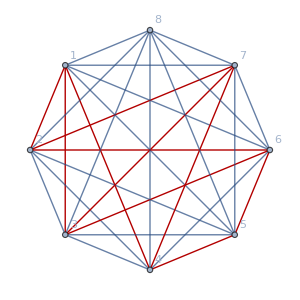
{True,0,False,452012}-Graphics-

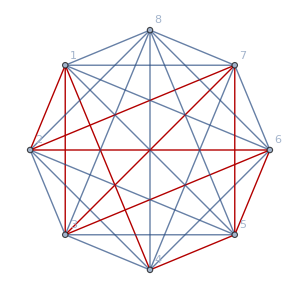
{True,0,False,452024}-Graphics-

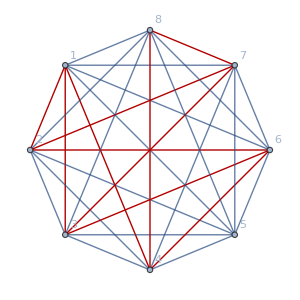
{True,0,False,452051}-Graphics-

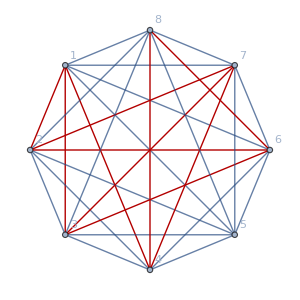
{True,0,False,452071}-Graphics-

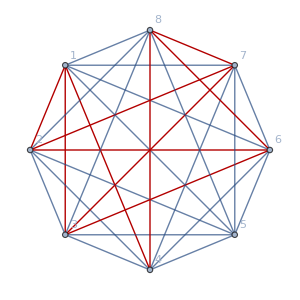
{True,0,False,452102}-Graphics-

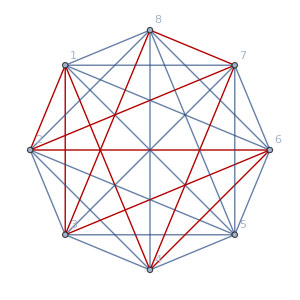
{True,0,False,452165}-Graphics-

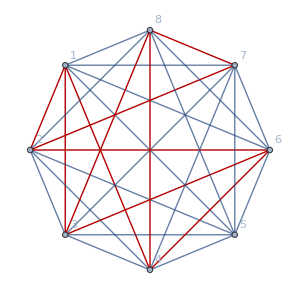
{True,0,False,452171}-Graphics-

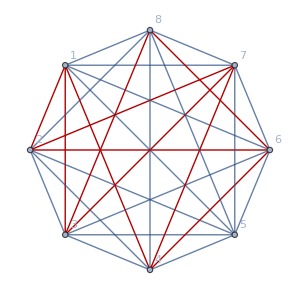
{True,0,False,452494}-Graphics-

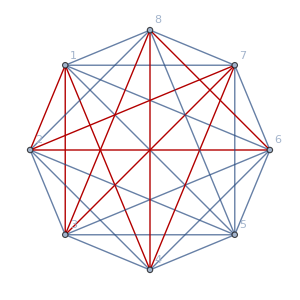
{True,0,False,452521}-Graphics-

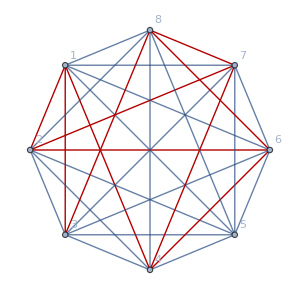
{True,0,False,452887}-Graphics-

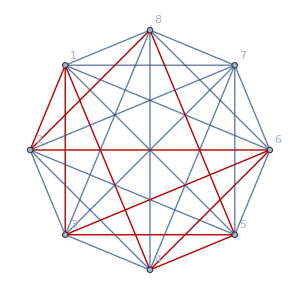
{True,0,False,454350}-Graphics-

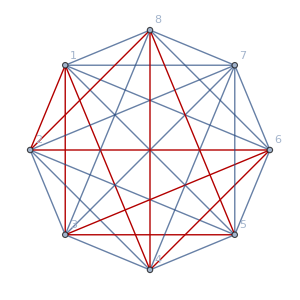
{True,0,False,454391}-Graphics-

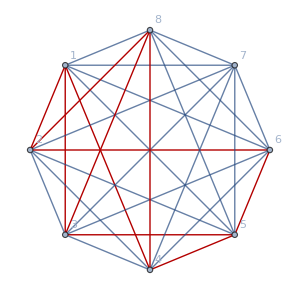
{True,0,False,454646}-Graphics-

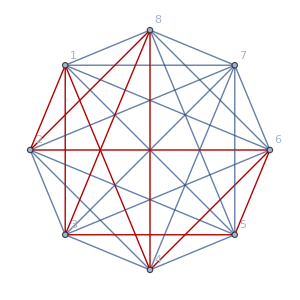
{True,0,False,454674}-Graphics-

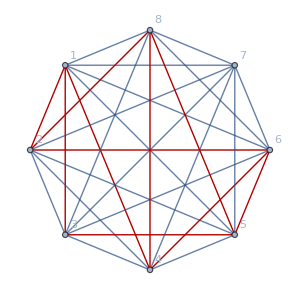
{True,0,False,454857}-Graphics-

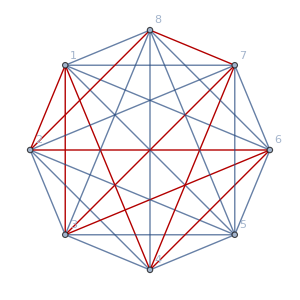
{True,0,False,455048}-Graphics-

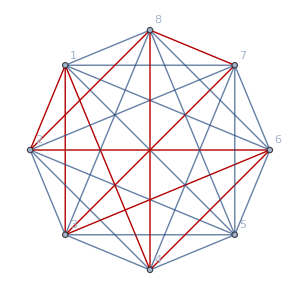
{True,0,False,455054}-Graphics-

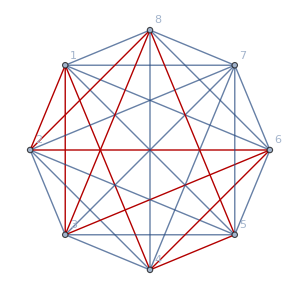
{True,0,False,455130}-Graphics-

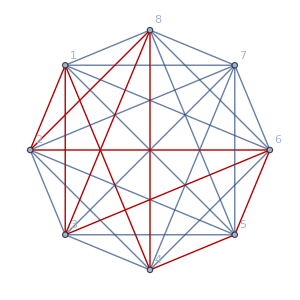
{True,0,False,455141}-Graphics-

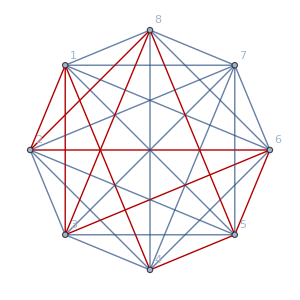
{True,0,False,455148}-Graphics-

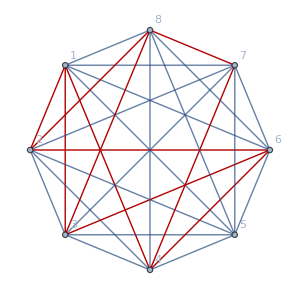
{True,0,False,455168}-Graphics-

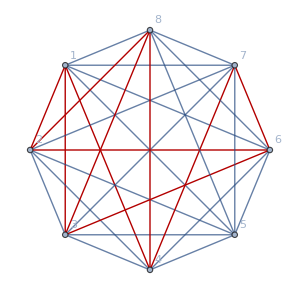
{True,0,False,455193}-Graphics-

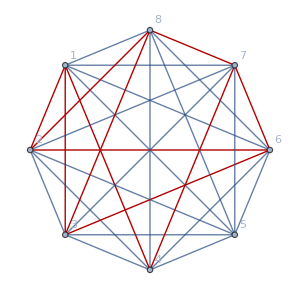
{True,0,False,455209}-Graphics-

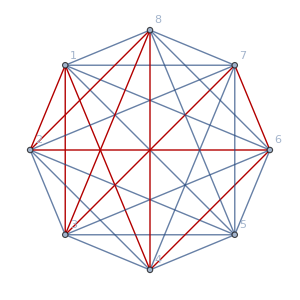
{True,0,False,455502}-Graphics-

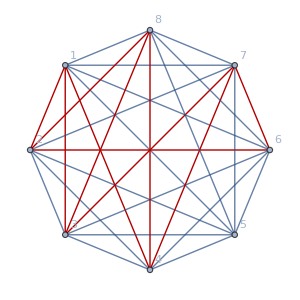
{True,0,False,455523}-Graphics-

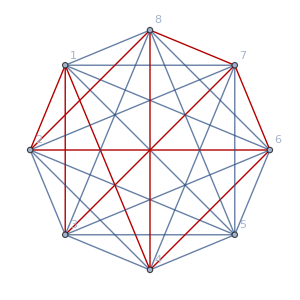
{True,0,False,455694}-Graphics-

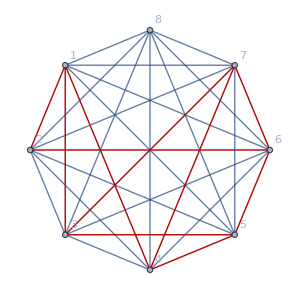
{True,0,False,458901}-Graphics-

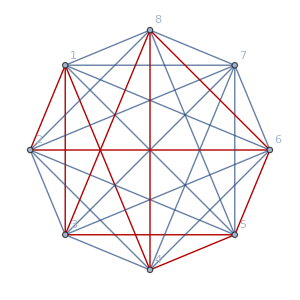
{True,0,False,459127}-Graphics-

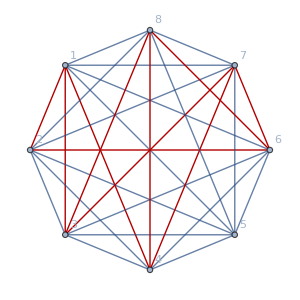
{True,0,False,460481}-Graphics-

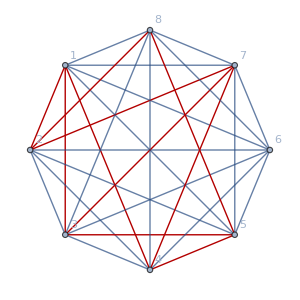
{True,0,False,462530}-Graphics-

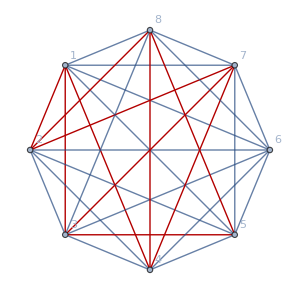
{True,0,False,462585}-Graphics-

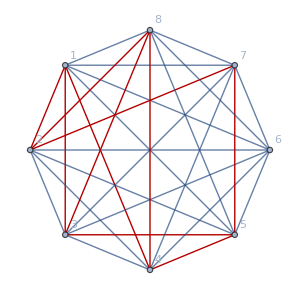
{True,0,False,462655}-Graphics-

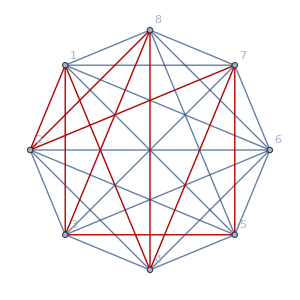
{True,0,False,462704}-Graphics-

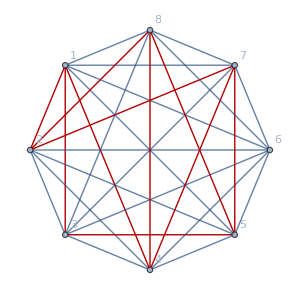
{True,0,False,462904}-Graphics-

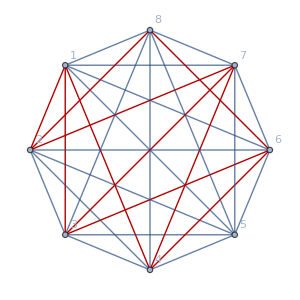
{True,0,False,463055}-Graphics-

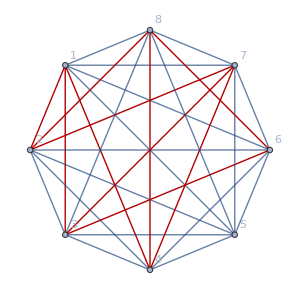
{True,0,False,463082}-Graphics-

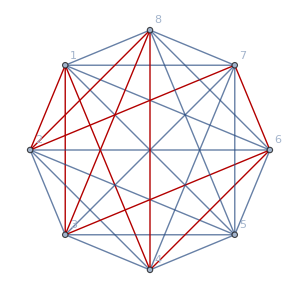
{True,0,False,463180}-Graphics-

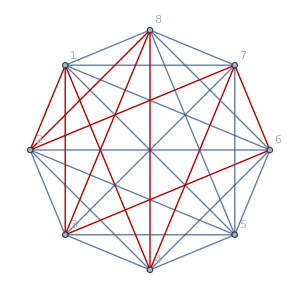
{True,0,False,463201}-Graphics-

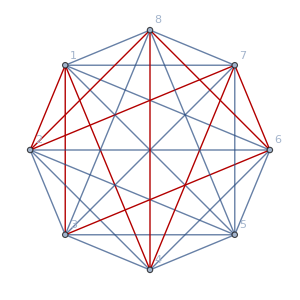
{True,0,False,463406}-Graphics-

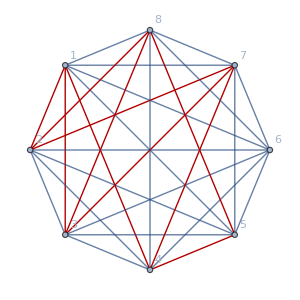
{True,0,False,463475}-Graphics-

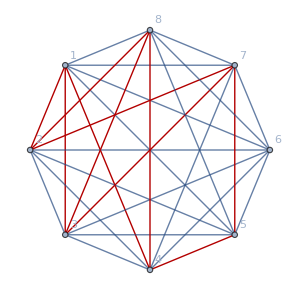
{True,0,False,463480}-Graphics-

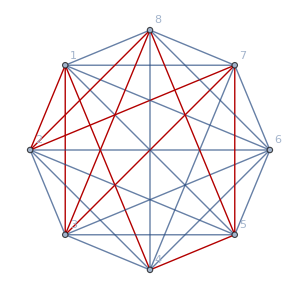
{True,0,False,463490}-Graphics-

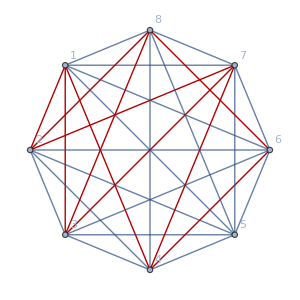
{True,0,False,463505}-Graphics-

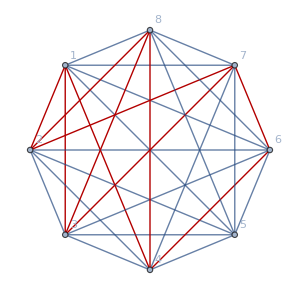
{True,0,False,463510}-Graphics-

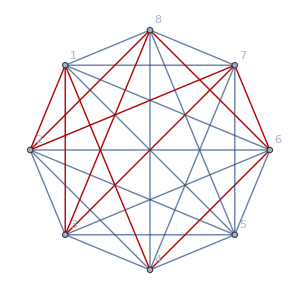
{True,0,False,463525}-Graphics-

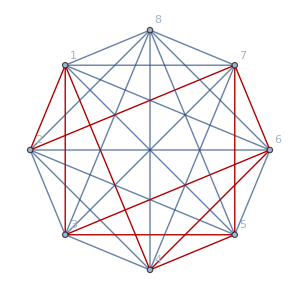
{True,0,False,466562}-Graphics-

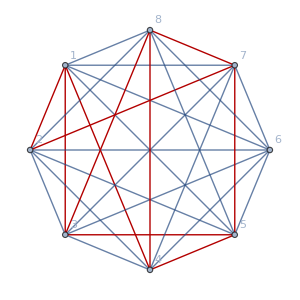
{True,0,False,467140}-Graphics-

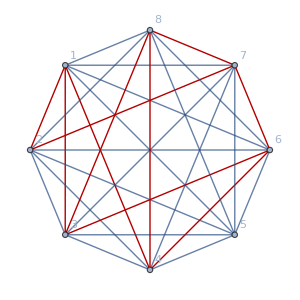
{True,0,False,467993}-Graphics-

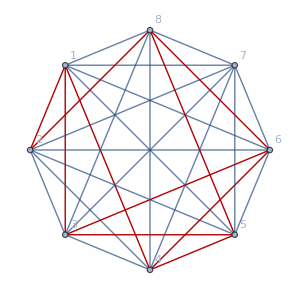
{True,0,False,471571}-Graphics-

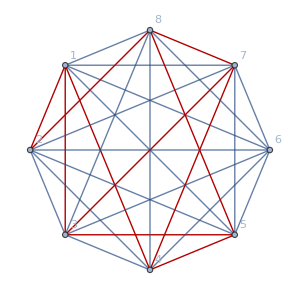
{True,0,False,471923}-Graphics-

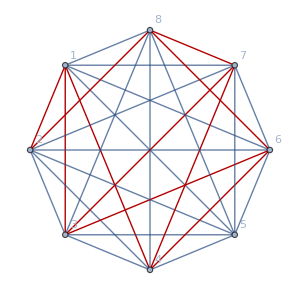
{True,0,False,472774}-Graphics-

$Aborted

```mathematica
Tally[Monitor[Table[
With[{prop={HasProperty[allGr8[[k]],7]&&HasProperty[allGr8[[k]],6]&&HasProperty[allGr8[[k]],5],ChromaticPolynomial[allGr8[[k]],4]/24,PlanarGraphQ[allGr8[[k]]],k}},
If[prop [[1]]&&prop[[2]]==0,Print[prop,ShowGr[allGr8[[k]]]]];prop
],{k,452012,Length[allGr8]}],Row[{k,ProgressIndicator[k/Length[allGr8]],Length[allGr8]}]],Most[#]&]
```

```mathematica
vals=Monitor[Table[
With[{prop={HasProperty[allGr8[[k]],7]&&HasProperty[allGr8[[k]],6]&&HasProperty[allGr8[[k]],5],ChromaticPolynomial[allGr8[[k]],4]/24,PlanarGraphQ[allGr8[[k]]],k}},
If[prop [[1]]&&prop[[2]]==0,allGr8[[k]],Null]
],{k,452012,472774}],Row[{k,ProgressIndicator[k/Length[allGr8]],Length[allGr8]}]];
```

```mathematica
Length[vals]
```

20763

```mathematica
vals2=Select[vals,#=!= Null&];Length[vals2]
```

51

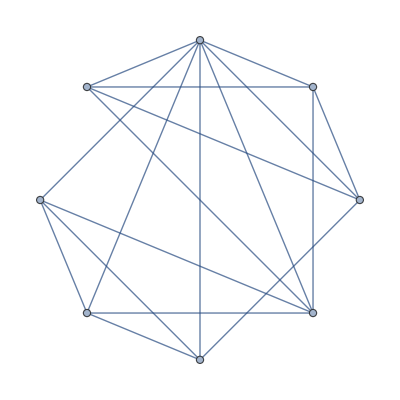
{{-Graphics-,51}}

```mathematica
Tally[vals2,IsomorphicGraphQ]
```

```mathematica
ShowGr[-Graphics-]
```

-Graphics-

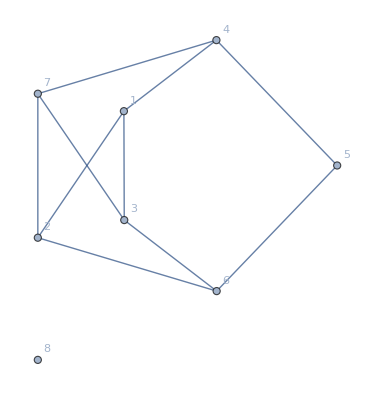

```mathematica
GraphComplement[-Graphics-,GraphLayout->"SpringElectricalEmbedding",VertexLabels->"Name"]
```